```mathematica
liouville[n_,z_]:=Product[(-1)^p[[2]] Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Grid[Table[{liouville[n,k]},{n,1,100},{k,-1,10}]]
```

{1} | {1} | {1} | {1} | {1} | {1} | {1} | {1} | {1} | {1} | {1} | {1}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {1} | {3} | {6} | {10} | {15} | {21} | {28} | {36} | {45} | {55}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-4} | {-10} | {-20} | {-35} | {-56} | {-84} | {-120} | {-165} | {-220}
{0} | {0} | {1} | {3} | {6} | {10} | {15} | {21} | {28} | {36} | {45} | {55}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {1} | {5} | {15} | {35} | {70} | {126} | {210} | {330} | {495} | {715}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {1} | {8} | {30} | {80} | {175} | {336} | {588} | {960} | {1485} | {2200}
{0} | {0} | {1} | {3} | {6} | {10} | {15} | {21} | {28} | {36} | {45} | {55}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {-1} | {-4} | {-10} | {-20} | {-35} | {-56} | {-84} | {-120} | {-165} | {-220}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{1} | {0} | {-1} | {-8} | {-27} | {-64} | {-125} | {-216} | {-343} | {-512} | {-729} | {-1000}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-6} | {-21} | {-56} | {-126} | {-252} | {-462} | {-792} | {-1287} | {-2002}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {1} | {9} | {36} | {100} | {225} | {441} | {784} | {1296} | {2025} | {3025}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {1} | {8} | {30} | {80} | {175} | {336} | {588} | {960} | {1485} | {2200}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{1} | {0} | {-1} | {-8} | {-27} | {-64} | {-125} | {-216} | {-343} | {-512} | {-729} | {-1000}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-10} | {-45} | {-140} | {-350} | {-756} | {-1470} | {-2640} | {-4455} | {-7150}
{0} | {0} | {1} | {3} | {6} | {10} | {15} | {21} | {28} | {36} | {45} | {55}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {1} | {8} | {30} | {80} | {175} | {336} | {588} | {960} | {1485} | {2200}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {1} | {8} | {30} | {80} | {175} | {336} | {588} | {960} | {1485} | {2200}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {1} | {12} | {54} | {160} | {375} | {756} | {1372} | {2304} | {3645} | {5500}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{0} | {0} | {1} | {7} | {28} | {84} | {210} | {462} | {924} | {1716} | {3003} | {5005}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {-1} | {-8} | {-27} | {-64} | {-125} | {-216} | {-343} | {-512} | {-729} | {-1000}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {-1} | {-8} | {-27} | {-64} | {-125} | {-216} | {-343} | {-512} | {-729} | {-1000}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-12} | {-60} | {-200} | {-525} | {-1176} | {-2352} | {-4320} | {-7425} | {-12100}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {-1} | {-8} | {-27} | {-64} | {-125} | {-216} | {-343} | {-512} | {-729} | {-1000}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-10} | {-45} | {-140} | {-350} | {-756} | {-1470} | {-2640} | {-4455} | {-7150}
{0} | {0} | {1} | {5} | {15} | {35} | {70} | {126} | {210} | {330} | {495} | {715}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {1} | {12} | {54} | {160} | {375} | {756} | {1372} | {2304} | {3645} | {5500}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {1} | {8} | {30} | {80} | {175} | {336} | {588} | {960} | {1485} | {2200}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {1} | {12} | {54} | {160} | {375} | {756} | {1372} | {2304} | {3645} | {5500}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{1} | {0} | {1} | {4} | {9} | {16} | {25} | {36} | {49} | {64} | {81} | {100}
{0} | {0} | {1} | {12} | {63} | {224} | {630} | {1512} | {3234} | {6336} | {11583} | {20020}
{1} | {0} | {-1} | {-2} | {-3} | {-4} | {-5} | {-6} | {-7} | {-8} | {-9} | {-10}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{0} | {0} | {-1} | {-6} | {-18} | {-40} | {-75} | {-126} | {-196} | {-288} | {-405} | {-550}
{0} | {0} | {1} | {9} | {36} | {100} | {225} | {441} | {784} | {1296} | {2025} | {3025}

```mathematica
liouville[n_,z_]:=Product[(-1)^p[[2]] Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Liou2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k,j] liouville[n,j],{j,0,k}]
LiouLinnik[n_]:=Sum[(-1)^(k+1)/k Liou2[n,k],{k,1,Log[2,n]}]
Table[{n,( LiouvilleLambda[n]),liouville[n,1],LiouLinnik[n]},{n,2,100}]//TableForm
```

2 | -1 | -1 | -1
3 | -1 | -1 | -1
4 | 1 | 1 | 1/2
5 | -1 | -1 | -1
6 | 1 | 1 | 0
7 | -1 | -1 | -1
8 | -1 | -1 | -1/3
9 | 1 | 1 | 1/2
10 | 1 | 1 | 0
11 | -1 | -1 | -1
12 | -1 | -1 | 0
13 | -1 | -1 | -1
14 | 1 | 1 | 0
15 | 1 | 1 | 0
16 | 1 | 1 | 1/4
17 | -1 | -1 | -1
18 | -1 | -1 | 0
19 | -1 | -1 | -1
20 | -1 | -1 | 0
21 | 1 | 1 | 0
22 | 1 | 1 | 0
23 | -1 | -1 | -1
24 | 1 | 1 | 0
25 | 1 | 1 | 1/2
26 | 1 | 1 | 0
27 | -1 | -1 | -1/3
28 | -1 | -1 | 0
29 | -1 | -1 | -1
30 | -1 | -1 | 0
31 | -1 | -1 | -1
32 | -1 | -1 | -1/5
33 | 1 | 1 | 0
34 | 1 | 1 | 0
35 | 1 | 1 | 0
36 | 1 | 1 | 0
37 | -1 | -1 | -1
38 | 1 | 1 | 0
39 | 1 | 1 | 0
40 | 1 | 1 | 0
41 | -1 | -1 | -1
42 | -1 | -1 | 0
43 | -1 | -1 | -1
44 | -1 | -1 | 0
45 | -1 | -1 | 0
46 | 1 | 1 | 0
47 | -1 | -1 | -1
48 | -1 | -1 | 0
49 | 1 | 1 | 1/2
50 | -1 | -1 | 0
51 | 1 | 1 | 0
52 | -1 | -1 | 0
53 | -1 | -1 | -1
54 | 1 | 1 | 0
55 | 1 | 1 | 0
56 | 1 | 1 | 0
57 | 1 | 1 | 0
58 | 1 | 1 | 0
59 | -1 | -1 | -1
60 | 1 | 1 | 0
61 | -1 | -1 | -1
62 | 1 | 1 | 0
63 | -1 | -1 | 0
64 | 1 | 1 | 1/6
65 | 1 | 1 | 0
66 | -1 | -1 | 0
67 | -1 | -1 | -1
68 | -1 | -1 | 0
69 | 1 | 1 | 0
70 | -1 | -1 | 0
71 | -1 | -1 | -1
72 | -1 | -1 | 0
73 | -1 | -1 | -1
74 | 1 | 1 | 0
75 | -1 | -1 | 0
76 | -1 | -1 | 0
77 | 1 | 1 | 0
78 | -1 | -1 | 0
79 | -1 | -1 | -1
80 | -1 | -1 | 0
81 | 1 | 1 | 1/4
82 | 1 | 1 | 0
83 | -1 | -1 | -1
84 | 1 | 1 | 0
85 | 1 | 1 | 0
86 | 1 | 1 | 0
87 | 1 | 1 | 0
88 | 1 | 1 | 0
89 | -1 | -1 | -1
90 | 1 | 1 | 0
91 | 1 | 1 | 0
92 | -1 | -1 | 0
93 | 1 | 1 | 0
94 | 1 | 1 | 0
95 | 1 | 1 | 0
96 | 1 | 1 | 0
97 | -1 | -1 | -1
98 | -1 | -1 | 0
99 | -1 | -1 | 0
100 | 1 | 1 | 0

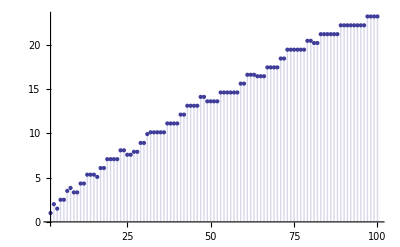

```mathematica
PI[n_, k_] := Sum[Abs[MoebiusMu[j]]( 1/k-PI[Floor[n/j],k+1]),{j,2,n}]
DiscretePlot[ PI[n,1],{n,2,100}]
```

```mathematica
PI[n_, k_] := Sum[LiouvilleLambda[j]( -1/k-PI[Floor[n/j],k+1]),{j,2,n}]
DiscretePlot[ PI[n,1],{n,2,100}]
```

-Graphics-

```mathematica
PI[n_, k_] := Sum[liouville[j,1]( -1/k-PI[Floor[n/j],k+1]),{j,2,n}]
DiscretePlot[ PI[n,1],{n,2,100}]
```

-Graphics-

```mathematica
ll[n_,z_]:=Product[(-1)^p[[2]] Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
l2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k,j] ll[n,j],{j,0,k}]
lLinnik[n_]:=Sum[(-1)^(k+1)/k l2[n,k],{k,1,Log[2,n]}]
Table[{n,lLinnik[n]},{n,2,100}]//TableForm
```